```mathematica
(*Load .csv file for Twist-3*)
```

```mathematica
twist3=Import["C:\\Users\\FAROOQ\\Videos\\Spin_quest\\September\\Papers\\29 Sept\\plot_digitizer\\Twist3.csv"];
```

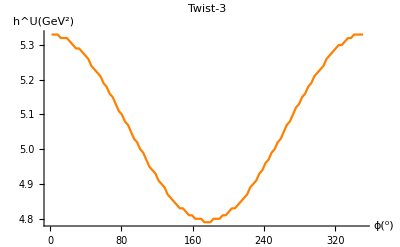

```mathematica
P1=ListLinePlot[twist3,PlotRange->All,PlotLabel->"Twist-3",AxesLabel->{"ϕ(^0)","h^U(GeV^2)"},PlotStyle->Orange]
```

```mathematica
(*Load .csv file for twist-4*)
```

```mathematica
twist4=Import["C:\\Users\\FAROOQ\\Videos\\Spin_quest\\September\\Papers\\29 Sept\\plot_digitizer\\Twist4.csv"];
```

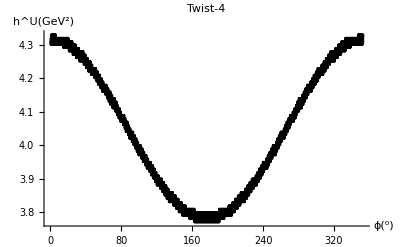

```mathematica
P2=ListLinePlot[twist4,PlotRange->All,PlotLabel->"Twist-4",AxesLabel->{"ϕ(^0)","h^U(GeV^2)"},PlotStyle->Black]
```

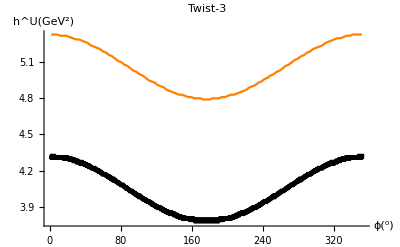

```mathematica
plot=Show[P1,P2,PlotRange->All,AxesOrigin->{0,0}]
```